```mathematica
A=208; (*Pb*)
Subscript[r, 0]=(1.12 A^(1/3)-0.86 A^(-1/3));(*fm*)
a=0.54 ;(*fm*)
Subscript[ρ, 0]=0.17;(*fm^-3*);
Subscript[σ, inel]=3;
ws[s_,z_]:=Subscript[ρ, 0]/(A(1+Exp[(√(s^2+z^2)-Subscript[r, 0])/a]));
ws1[s1_,s2_,ang_,z_]:=Subscript[ρ, 0]/(A(1+Exp[(√(s1^2+s2^2-2s1 s2 Cos[ang]+z^2)-Subscript[r, 0])/a]));
```

```mathematica
NIntegrate[2π s ws[s,z],{s,0,∞},{z,-∞,∞}]
```

1.00017

```mathematica
T[s_]:=NIntegrate[ws[s,z],{z,-∞,∞}]
T1[s1_,s2_,ang_]:=NIntegrate[ws1[s1,s2,ang,z],{z,-∞,∞}]
```

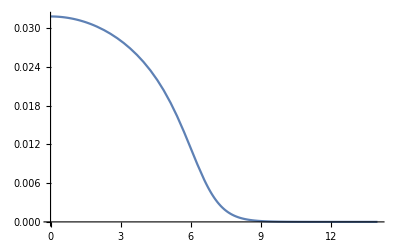

```mathematica
Plot[Subscript[σ, inel] T[x],{x,0,14}]
```

```mathematica
Quiet[NIntegrate[2π x T[x],{x,0,∞}]]
```

1.00017

```mathematica
Npart[b_]:=2 A Quiet[NIntegrate[s T1[s,b,ang](1-(1-Subscript[σ, inel] T[s])^A),{s,0,∞},{ang,0,2 π}]]
```

```mathematica
NpartTab=Flatten[Join[{Table[{i,0},{i,0,2,0.1}],Table[{i,0},{i,2.5,12,0.5}],Table[{i,0},{i,12.1,15,0.1}]}],1]
SetSharedVariable[NpartTab];
```

{{0.,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1.,0},{1.1,0},{1.2,0},{1.3,0},{1.4,0},{1.5,0},{1.6,0},{1.7,0},{1.8,0},{1.9,0},{2.,0},{2.5,0},{3.,0},{3.5,0},{4.,0},{4.5,0},{5.,0},{5.5,0},{6.,0},{6.5,0},{7.,0},{7.5,0},{8.,0},{8.5,0},{9.,0},{9.5,0},{10.,0},{10.5,0},{11.,0},{11.5,0},{12.,0},{12.1,0},{12.2,0},{12.3,0},{12.4,0},{12.5,0},{12.6,0},{12.7,0},{12.8,0},{12.9,0},{13.,0},{13.1,0},{13.2,0},{13.3,0},{13.4,0},{13.5,0},{13.6,0},{13.7,0},{13.8,0},{13.9,0},{14.,0},{14.1,0},{14.2,0},{14.3,0},{14.4,0},{14.5,0},{14.6,0},{14.7,0},{14.8,0},{14.9,0},{15.,0}}

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
ParallelDo[NpartTab[[i,2]]=Npart[NpartTab[[i,1]]],{i,Length[NpartTab]}]
```

```mathematica
NpartTab
```

```mathematica
NpartTab={{0.,392.10661525092314},{0.1,392.0376169586617},{0.2,391.82213814614965},{0.30000000000000004,391.4863659978713},{0.4,391.00471472707557},{0.5,390.3864664190645},{0.6000000000000001,389.63239753850996},{0.7000000000000001,388.7434700521212},{0.8,387.72084504072393},{0.9,386.5658765119421},{1.,385.2801189422648},{1.1,383.8653118861333},{1.2000000000000002,382.32344323714824},{1.3,380.65663846247145},{1.4000000000000001,378.86725071670025},{1.5,376.95782768357947},{1.6,374.9310223242259},{1.7000000000000002,372.7896293550774},{1.8,370.5367260066498},{1.9000000000000001,368.1753629425881},{2.,365.70875293030514},{2.5,351.9136699683929},{3.,335.99503638381003},{3.5,318.3713809222181},{4.,299.4302188834107},{4.5,279.5181819230327},{5.,258.9427011435945},{5.5,237.97702760022497},{6.,216.86692077748094},{6.5,195.83634044150475},{7.,175.09211096996378},{7.5,154.8274839259432},{8.,135.2247567923185},{8.5,116.45738602454384},{9.,98.69127336575991},{9.5,82.08559534193168},{10.,66.79291057693845},{10.5,52.9580154384056},{11.,40.71445725159219},{11.5,30.176655047536315},{12.,21.424393537235584},{12.1,19.89136055439546},{12.2,18.430615469201097},{12.299999999999999,17.04177931076858},{12.4,15.724302223660182},{12.5,14.477459248632027},{12.6,13.300338969630355},{12.7,12.191841753473668},{12.799999999999999,11.150675848335096},{12.9,10.175357798507232},{13.,9.264216105027682},{13.1,8.415397909381054},{13.2,7.626878797793684},{13.3,6.896476152143431},{13.4,6.221864997752891},{13.5,5.6005988556349555},{13.6,5.030127977834815},{13.7,4.50782505813882},{13.8,4.031008171554294},{13.9,3.596965791525404},{14.,3.2029808382024347},{14.1,2.846354268880739},{14.2,2.524427628804999},{14.3,2.234615684154768},{14.4,1.974371786355733},{14.5,1.7412830955786476},{14.6,1.5330299315084412},{14.7,1.3474090664927063},{14.8,1.1823410339116642},{14.9,1.0358752081042},{15.,0.906191693052112}};
```

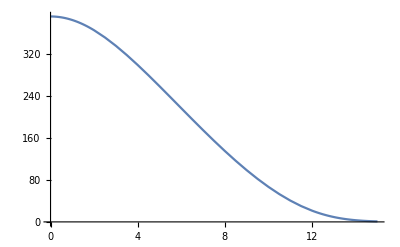

```mathematica
ListPlot[NpartTab,Joined->True]
```

```mathematica
Npartinter=Interpolation[NpartTab];
```

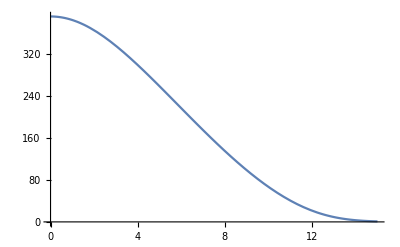

```mathematica
Plot[Npartinter[x],{x,0,15}]
```